```mathematica
numberOfAgents = 100;
donationCost = -10;
buyCost = -40;
donationHealthChange=7;
usageUtil = 5;
waitCost = -1;
fullToolHealth=10;

agentParams = Array[Function[x,
{(*RandomReal[0.4], (* How often a tool is needed *)*)
0.3,
RandomReal[0.05], (* Prob to buy tool *)
RandomReal[0.2], (* Prob to donate *)
0, (* Has tool (tool health) *)
0 (* payoff *)
}],numberOfAgents];
```

```mathematica
(* Returns the utility, the updated agent, and change in poolHealth.
int, agent, int *)
CalculatePayoff[agent_,nPTools_]:=Module[
{p=agent[[1]],pb=agent[[2]],
pd=agent[[3]],toolHealth=agent[[4]],
util=agent[[5]],poolHealthChange=0},
If[RandomReal[]<p,
If[toolHealth>0,
util+=usageUtil; toolHealth-=1,
If[RandomReal[]<pb,
toolHealth=fullToolHealth;
util+=buyCost+usageUtil,
If[nPTools>0,
util+=usageUtil;poolHealthChange-=1,
util+=waitCost]
]
],
If[RandomReal[]<pd,
poolHealthChange+=donationHealthChange;
util+=donationCost,
util+=0
]
];
{{p,pb,pd,toolHealth,util},poolHealthChange}
];

CalculatePayoff[{0,0,1,5,0},3]
```

{{0,0,1,5,-10},7}

```mathematica
MutateValue[v_] := Module[{value},
If[v>0.5,distance = 1-v,distance =v];
value=RandomVariate[NormalDistribution[v,(*distance/4)+*)0.1]];
If[value<=0,0,Min[value,1]]
];
MutateValue[0.1]
MutateAgent[agent_]:=Module[
{p=agent[[1]],pb=agent[[2]],pd=agent[[3]]},
{p,MutateValue[pb],MutateValue[pd],0,0}
];
```

0.219218

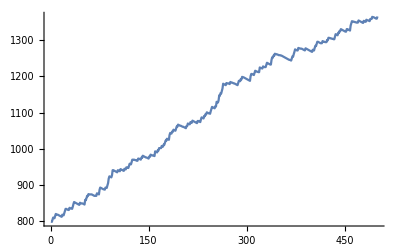

{{0.3,0.436845,0.00579242,1,229},{0.3,0.830073,0,0,227},{0.3,0.987605,0,4,220},{0.3,0.781592,0,5,219},{0.3,0.987605,0,2,215},{0.3,0.389731,0.0253397,1,215},{0.3,0.853526,0,2,213},{0.3,0.436845,0.00579242,0,213},{0.3,0.830073,0,2,211},{0.3,0.830073,0,3,210},{0.3,0.830073,0,0,209},{0.3,0.584133,0,1,208},{0.3,0.853526,0,1,208},{0.3,0.436845,0.00579242,6,208},{0.3,0.436845,0.00579242,9,206},{0.3,0.436845,0.00579242,0,205},{0.3,0.436845,0.00579242,6,204},{0.3,0.436845,0.00579242,8,201},{0.3,0.830073,0,7,200},{0.3,0.436845,0.00579242,9,200},{0.3,0.830073,0,2,199},{0.3,0.436845,0.00579242,1,198},{0.3,0.436845,0.00579242,0,198},{0.3,0.436845,0.00579242,0,198},{0.3,0.830073,0,4,197},{0.3,0.436845,0.00579242,4,196},{0.3,0.82395,0,0,195},{0.3,0.830073,0,3,195},{0.3,0.436845,0.00579242,7,195},{0.3,0.830073,0,7,194},{0.3,0.647613,0,0,194},{0.3,0.88906,0,0,194},{0.3,0.830073,0,4,194},{0.3,0.82395,0,6,194},{0.3,0.830073,0,7,194},{0.3,0.436845,0.00579242,4,194},{0.3,0.853526,0,0,193},{0.3,0.584133,0,0,193},{0.3,0.88906,0,3,192},{0.3,0.853526,0,3,191},{0.3,0.987605,0,4,190},{0.3,0.830073,0,10,189},{0.3,0.830073,0,1,189},{0.3,0.830073,0,3,189},{0.3,0.830073,0,8,189},{0.3,0.853526,0,2,189},{0.3,0.436845,0.00579242,6,189},{0.3,0.830073,0,4,188},{0.3,0.830073,0,2,187},{0.3,0.436845,0.00579242,0,187},{0.3,0.830073,0,4,186},{0.3,0.830073,0,7,185},{0.3,0.866981,0,6,184},{0.3,0.436845,0.00579242,4,184},{0.3,0.481346,0,1,182},{0.3,0.436845,0.00579242,9,182},{0.3,0.88906,0,5,181},{0.3,0.830073,0,9,181},{0.3,0.830073,0,6,181},{0.3,0.436845,0.00579242,8,181},{0.3,0.436845,0.00579242,6,181},{0.3,0.830073,0,4,180},{0.3,0.436845,0.00579242,10,180},{0.3,0.436845,0.00579242,0,180},{0.3,0.853526,0,1,179},{0.3,0.866981,0,5,179},{0.3,0.830073,0,9,179},{0.3,0.830073,0,9,178},{0.3,0.436845,0.00579242,9,177},{0.3,0.830073,0,6,176},{0.3,0.987605,0,7,175},{0.3,0.830073,0,8,174},{0.3,0.436845,0.00579242,4,174},{0.3,0.830073,0,10,173},{0.3,0.436845,0.00579242,8,173},{0.3,0.830073,0,2,172},{0.3,0.830073,0,10,172},{0.3,0.830073,0,7,171},{0.3,0.436845,0.00579242,5,171},{0.3,0.830073,0,6,170},{0.3,0.830073,0,4,170},{0.3,0.853526,0,9,170},{0.3,0.436845,0.00579242,8,168},{0.3,0.436845,0.00579242,2,165},{0.3,0.830073,0,4,164},{0.3,0.853526,0,8,163},{0.3,0.88906,0,9,163},{0.3,0.830073,0,10,160},{0.3,0.830073,0,10,157},{0.3,0.436845,0.00579242,7,156},{0.3,0.436845,0.00579242,1,155},{0.3,0.830073,0,10,154},{0.3,0.436845,0.00579242,10,151},{0.3,0.436845,0.00579242,5,149},{0.3,0.830073,0,9,148},{0.3,0.830073,0,4,148},{0.3,0.830073,0,10,145},{0.3,0.481346,0,8,139},{0.3,0.436845,0.00579242,0,138},{0.3,0.82257,0.157229,4,-395}}

```mathematica
DoRound[agentList_,initPoolHealth_,iterations_]:=Module[
{poolHealth=initPoolHealth,
agents=agentList,
agentPayoffs=ConstantArray[0,Length[agentList]],
PHhistory = {}},
For[i=0,i<iterations,i++,
nPoolTools=poolHealth/fullToolHealth;
(*agents=RandomSample[agents];*)
agents=Sort[agents,#1[[3]]>#2[[3]]&];
For[j=1,j≤Length[agents],j++,
{newAgent, healthChange}=CalculatePayoff[agents[[j]],nPoolTools];
agents[[j]]=newAgent;
poolHealth+=healthChange;
nPoolTools=If[healthChange==-1,healthChange,nPoolTools];
];

PHhistory = Append[PHhistory,poolHealth];
];
{agents, PHhistory}
];

RunSim[agentList_]:=Module[{agents=agentList,history={}},
For[k=1,k<100,k++,
{ag, ph} =DoRound[agents,800,500];
Print[k];
(*Print[Map[Function[a,Last[a]],ag]];*)
rankedAgents=Sort[ag,Last[#1]>Last[#2]&];
newAgents=Take[rankedAgents,Length[rankedAgents]/2];
newAgents=Join[newAgents,newAgents];
newAgents=Map[Function[a,{a[[1]],a[[2]],a[[3]],0,0}],newAgents];
(* Mutate agents *)
newAgents=Map[Function[a,If[RandomReal[]<0.05,MutateAgent[a],a]],newAgents];
agents=newAgents;
history=Append[history, ph];
];
{ag, ph} =DoRound[agents,800,500];
history=Append[history, ph];
{ag, history}
];

{a,h}=RunSim[agentParams];
ListLinePlot[h[[-1]]]
Sort[a,Last[#1]>Last[#2]&]
```